Created by: ruebenko on 02-26-2021 09:11:57

### Categorization

Tutorial

OpenCascadeLink

OpenCascadeLink`

OpenCascadeLink/tutorial/SurgicalFixationPlate

Synonyms

CAD

### Keywords

fillet

chamfer

Details

# Surgical fixation plate

The purpose of this notebook is to illustrate the usage of the OpenCascadeLink to create a surgical fixation plate based on a parametric design.

A surgical fixation plate is a medical device used to stabilize and support broken bones during the healing process. Titanium fixation plates, particularly those designed for the forearm, are favored for their strength, biocompatibility, and resistance to corrosion. These plates are surgically attached to the fractured bones using screws, ensuring proper alignment and promoting effective recovery. The usage of a parametric design allows for optimization procedures and easy personalization of the devices based on the patients needs.

The fixation plate design is based on an analytical description that leads to a parametric geometry function of the fixation plate's side length and the width. The creation procedure in OpenCascade starts with the description of the planar face which is then extruded to form the 3D object.

-Graphics3D-

Surgical fixation plate (in brown) placed over the Radius in the forearm.

```mathematica
graphicsPlate=-Graphics3D-;
rotatedMR=Rotate[
Rotate[
Translate[
Rotate[
Rotate[
Scale[graphicsPlate,700]
,Pi/2,{0,1,0}]
,Pi/2,{0,0,1}]
,tt={251,-100,900}]
,-12Degree,{1,0,0},tt]
,-9 Degree,{0,1,0},tt];
edgeframeRotatedMR=Show[
Graphics3D[
{EdgeForm[],FaceForm[Brown],rotatedMR}
],NDSolve`FEM`ToBoundaryMesh[rotatedMR]["Edgeframe"]];
plot=Show[
partList=Entity["AnatomicalStructure","LeftForearm"]["ConstitutionalParts"];AnatomyPlot3D[Style[#,Opacity[0.05]]&/@{
Entity["AnatomicalStructure","SkinOfLeftForearm"],Pick[partList,MemberQ[#["EntityClasses"],EntityClass["AnatomicalStructure","Muscles"]]&/@partList,True],
Entity["AnatomicalStructure","LeftHand"]
},PlotTheme->"Monochrome"],
AnatomyPlot3D[{Entity["AnatomicalStructure","LeftRadius"],Entity["AnatomicalStructure","LeftUlna"]},Lighting->"Neutral"],
edgeframeRotatedMR,ViewVertical->{1,0,0},PlotRange->{{185,314},{-155,-25.},{730,970}},ViewPoint->Front]
```

Load the packages:

```mathematica
Needs["OpenCascadeLink`"]
Needs["NDSolve`FEM`"]
```

## Geometry

The fixation plate is divided into a central section and two fixation sections at the sides. Both the fixation sections and the central section have three holes each.

-Graphics-

Two dimensional technical diagram of the planar surgical fixation plate with sizes expressed as a function of the desired length and width. The fixation plate is divided into three sections, each with a length of length/3.

```mathematica
coord2D=;
holeCC=;
width=1;
length=16;
Show[
(* right circle *)
Translate[Region[Style[ImplicitRegion[(x)^2+(y-width/2)^2==1,{x,y}],
myBlue=RGBColor[0.44,0.59,1]
(*myBlue=RGBColor[0.77,0.77,0.77]*)]],{length-width/2,-width}],
Graphics[{Gray,Text["⌀ 2 width",{0.98length,-2width}],FaceForm[myBlue],EdgeForm[myBlue],Disk[{length-xampl,-width/2},0.05],}],
(*left Sin mark*)
Translate[Region[Style[ImplicitRegion[(x)^2+(y)^2==(0.1)^2,{x,y}],
myBlue]],leftSineMarkCircle={length/6,-0.01}],
Graphics[{myBlue, Line[{leftSineMarkCircle+0.1,leftSinePos=leftSineMarkCircle+(shift={length/20,width})}],
Gray,Text["Sin[πx/ϕ]",leftSinePos+{0.8,0.3}]
}
],

(*central Sin mark*)
Translate[Region[Style[ImplicitRegion[(x)^2+(y)^2==(0.1)^2,{x,y}],
myBlue]],centralSineMarkCircle={length/2-length/20,+0.12}],
Graphics[{myBlue, Line[{centralSineMarkCircle+0.1,leftSinePos=centralSineMarkCircle+shift}],
Gray,Text["Sin[πx/6ϕ]",leftSinePos+{1,0.3}]
}
],

Graphics[{
FaceForm[],EdgeForm[Black],
Line[{{0,2width},{length,2 width}}],

(* bottom lines *)
Line[{{0-width+width/2,-3width+0.2},{0-width+width/2,-3 width-0.2}}],
Line[{{length+width/2,-3width+0.2},{length+width/2,-3 width-0.2}}],

Line[{{0,-3width+0.2},{0,-3 width-0.2}}],
Line[{{length,-3width+0.2},{length,-3 width-0.2}}],
Line[{{0-width+width/2,-3width},{length+width/2,-3width}}],
{Dashed,Thin,Line[{{0,2 width},{0,-3 width-0.1}}],
Line[{{length,2 width},{length,-3 width-0.1}}],
Line[{{length/3,2 width},{length/3,0}}],
Line[{{2length/3,2 width},{2length/3,0}}]
},



{Thick,BSplineCurve[coord2D,SplineDegree->1],
BSplineCurve[holeCC,SplineDegree->1]},

(* add the shift *)

(* right markers *)

{myBlue, 
{Dashed,Line[{{length/3 1/(3*2*2),waveAmplitude=0.15},{-length/16,waveAmplitude}}],
 Line[{{xampl=length/3 1/(3*2*2),waveAmplitude},{xampl,-waveAmplitude}}],
Line[{{3xampl,-waveAmplitude},{-length/16,-waveAmplitude}}]},
Line[{{-length/17,waveAmplitude},{-length/17,-waveAmplitude}}]

},{Gray,Text["wave \n amplitude",{-1.2length/10,0}]},

{Gray,Text["length",{length/2,-3.4width}],
Text["length / 3",{length/2,2.3width}],
Text["length / 3",{length(1/6),2.3width}],
Text["length / 3",{length(5/6),2.3width}]
},
{
myBlue,Arrowheads[0.015],Arrow[{rMark={length/6,-2width},{5xampl,-width+0.2}}],
FaceForm[myBlue],EdgeForm[myBlue],Disk[{xampl,-width/2},0.05],
Arrow[{rMark,{xampl,-width+0.2}}],
Arrow[{rMark,{9xampl,-width+0.2}}],
Gray,Text["⌀ 2*r_hole",rMark+0.3*{1,-1} ]
},

{myBlue, 
Line[{{length/2,-width/2},{length/2,-2width}}],
Line[{{length/2-(ll=length/10),-width/2},{length/2-ll,-2width}}],
Line[{{length/2-ll-0.1,-2 width},{length/2+0.1,-2width}}],
Gray,Text["length/10",{length/2-ll/2,-2.5width}],

myBlue,
Translate[(rotLine=Rotate[Line[{{length/2+ll,-2 width},{length/2+ll,-width/2}}],-π/4]),{-0.7,+0.3}],
Translate[rotLine,{-0.4,0.14}],

{Dashed,Translate[Scale[(perpLine=Rotate[rotLine,π/2]),0.5],{-0.9,-0.4}]},
{Gray,
Text["b",{length/2+ll-0.4,-2.1width}]},

Translate[Scale[perpLine,1],{0.7,0.6}],
Translate[Scale[perpLine,1],{0.2,0.1}],
{Dashed,Translate[Scale[rotLine,0.8],{0.7,-0.42}]},
{Gray,
Text["a",{length/2+ll+0.6,-2.1width}]}
},

{myBlue,Point[{length/2,-width/2}],
Point[{length/2-ll,-width/2}],
Point[{length/2+ll,-width/2}]},

{Gray,Text["2 ϕ", {length-7xampl,1.3 width}],
myBlue, Line[{{length-5xampl,width-0.1},{length-9xampl,width-0.1}}],
(*Dashed,*)
Line[{{length-9xampl,0.2},{length-9xampl,width}}],
Line[{{length-5 xampl,0.2},{length-5 xampl,width}}]},

{myBlue,
Text["central holes",{length/2,3width}],
Text["fixation holes",{length(1/6),3width}],
Text["fixation holes",{length(5/6),3width}],
Line[{{0+0.2,2.5width},{0+0.2,2.75width},{-0.2+length/3,2.75width},{-0.2+length/3,2.5width}}],
Line[{{length/3+0.2,2.5width},{length/3+0.2,2.75width},{-0.2+2length/3,2.75width},{-0.2+2length/3,2.5width}}],
Line[{{2length/3+0.2,2.5width},{2length/3+0.2,2.75width},{-0.2+length,2.75width},{-0.2+length,2.5width}}]
}

}]
]
```

To create the 3D geometry a 2D draft will be made that then can be extruded to 3D. To make this 2D draft, all edges will be parameterized and connected to form a planar 2D face. From that face the holes can be removed and in the last step the perforated face will be extruded to 3D.

The first step is to create the top edge of the 2D plate. This long edge can be split in three regions represented by a sine function scaled to fit the desired numbers of holes in each semi-period. The geometric properties are expressed in centimeters.

Specify geometric parameters:

```mathematica
length=16;
thickness=0.3;
width=1;
waveAmplitude=0.15;
```

Specify the holes properties:

```mathematica
numberFixationHoles=3;
radiusFixationHoles=0.3;
```

A sine function is used to house the holes of the fixation plate within each positive wave cycle of the period. The period is determined by dividing the available length by twice the number of fixation holes.

Compute the scale factor ϕ for the fixation edge period:

```mathematica
ϕ=length/3 1/(numberFixationHoles*2)
```

8/9

Create an auxiliary parametric function for the fixation holes section of the edge:

```mathematica
fixationEdge[x_]:=Sin[(π x)/ϕ]
```

Create a scaled auxiliary function for the central holes section of the edge:

```mathematica
centralEdge[x_]:=fixationEdge[x/6]
```

Assemble the auxiliary function representing half of the top edge:

```mathematica
edge[x_]:=width/2+waveAmplitude*Which[
x<=length/3,fixationEdge[x],
length/3<x<=length/2,-centralEdge[x]]
```

Visualize the top edge:

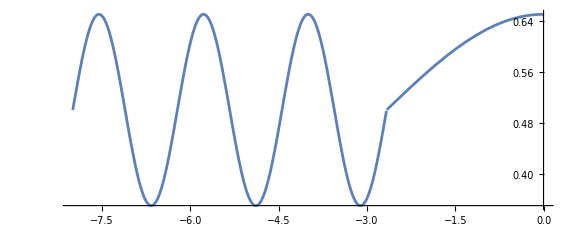

```mathematica
edgePlot=Plot[edge[x+length/2],{x,-length/2,0},AspectRatio->Automatic,ImageSize->Large,Ticks->{True,False}]
```

The next step is to convert this plot of the edge into a spline. For that the edge is discretized and downsampled and converted to a BSplineCurve.

Discretize the edge:

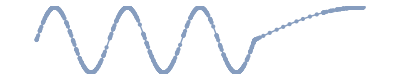

```mathematica
discretedEdge=DiscretizeGraphics[edgePlot]
```

Reduce the number of coordinates by choosing every 15th coordinate:

```mathematica
topEdgeCoords=MeshCoordinates[discretedEdge][[1;;-1;;15]];
```

Make sure the rightmost point is on the axis of symmetry at x=0:

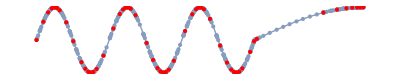

```mathematica
topEdgeCoords[[-1,1]]=0.;Show[discretedEdge,Graphics[{Red,Point[topEdgeCoords]}]]
```

Create and visualize the spline to represent half of the top edge:

```mathematica
topEdgeSpline=BSplineCurve[topEdgeCoords];
Graphics[topEdgeSpline]
```

-Graphics-

The next step is to create left edge of the geometry, which can be represented by a circular sector. The challenge is to find the exact size of the sector. To help in the process it is convenient to visualize a half circle and the top edge and an extension of the top edge that intersects with the half circle.

Define the center of the circle for the left edge:

```mathematica
leftCircleCenter={-length/2+width/2,0}
```

{-15/2,0}

Define a circle between π/2 and 3π/2:

```mathematica
circleSegement=Circle[leftCircleCenter,width,{π/2,π}]
```

Circle[{-15/2,0},1,{π/2,π}]

Define an extension line from the top edge through the half circle:

```mathematica
extensionLine=Line[{topEdgeCoords[[1]],{leftCircleCenter[[1]]-width,topEdgeCoords[[1,2]]}}]
```

Line[{{-8.,0.5},{-17/2,0.5}}]

Visualizing the top edge, the extension line and the half circle:

```mathematica
Graphics[{topEdgeSpline,{Red,extensionLine},circleSegement}]
```

-Graphics-

Once the intersection of the extension line and the half circle is computed the left edge sector can be established.

Compute the intersection of the extension of the top edge and the right edge:

```mathematica
intersectionPoint=RegionIntersection[extensionLine,circleSegement]
```

Point[{{-8.36603,0.5}}]

Extract the intersection coordinate:

```mathematica
leftIntersectionCoord=intersectionPoint[[1,1]]
```

{-8.36603,0.5}

Compute the angle of the left circular sector:

```mathematica
leftIntersectAngle=NSolveValues[leftIntersectionCoord[[1]]==leftCircleCenter[[1]]+width*Cos[θ],θ,MaxRoots->1][[1]]
```

3.66519

Visualizing the top edge, the extension edge and the left edge:

```mathematica
leftLine=Line[{leftIntersectionCoord,topEdgeCoords[[1]]}];
leftEdge=Circle[leftCircleCenter,width,{2π-leftIntersectAngle,π}];
Graphics[{topEdgeSpline,{Red,leftLine},leftEdge}]
```

-Graphics-

Create a reflection transform with respect to the y axis:

```mathematica
rt1=ReflectionTransform[{1,0},{0,0}];
```

Transform and visualize the edges:

```mathematica
tr1=TransformedRegion[topEdgeSpline,rt1];
tr2=TransformedRegion[leftLine,rt1];
tr3=TransformedRegion[leftEdge,rt1];
tr3=tr3/.Circle[c_List,r_,s_]:>Circle[c,r,{0,s[[1]]}];
Graphics[{topEdgeSpline,leftLine,leftEdge,{Blue,tr1},{Red,tr2},{Magenta,tr3}}]
```

-Graphics-

bug: 451502. Also important is that the circle goes from 0 to s[[1]] and not the other way.

Convert the edges to OpenCascade:

```mathematica
e1=OpenCascadeShape[leftEdge];
e2=OpenCascadeShape[leftLine];
e3=OpenCascadeShape[topEdgeSpline];
e4=OpenCascadeShape[tr1];
e5=OpenCascadeShape[tr2];
e6=OpenCascadeShape[tr3];
```

Combine the edges into a single wire:

```mathematica
w1=OpenCascadeShapeWire[{e1,e2,e3,e4,e5,e6}]
```

OpenCascadeShapeExpression[7]

Next, the entire top half will be reflected to the bottom.

Create a reflection transform for the top half to the bottom:

```mathematica
rt2=ReflectionTransform[{0,-1},{0,0}];
```

Visualize the transformation of the top half to the bottom half:

```mathematica
gt1=GeometricTransformation[topEdgeSpline,rt2];
gt2=GeometricTransformation[leftLine,rt2];
gt3=GeometricTransformation[leftEdge,rt2];
Graphics[{topEdgeSpline,leftLine,leftEdge,{Blue,gt1},{Red,gt2},{Magenta,gt3}}]
```

-Graphics-

The actual transformation will operate on the entire top edge.

Reflect the entire top shape to the bottom:

```mathematica
w2=OpenCascadeShapeTransformation[w1,rt2]
```

OpenCascadeShapeExpression[8]

Create a face from the top and bottom shapes:

```mathematica
face=OpenCascadeShapeFace[{w1,w2}]
```

OpenCascadeShapeExpression[9]

Visualize the boundary mesh:

```mathematica
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[face];
bmesh["Wireframe"]
```

-Graphics3D-

The next step is to introduce the holes in the fixation plate. There are three group of holes: two groups of fixation holes and the central holes. The fixation holes are described by circles aligned with the sine spatial period ϕ, while the central holes are represented by an hyperelliptic boundary described below.

Compute the distance of the holes based on the sine period:

```mathematica
holesCentersAlongX=Table[-length/2+(2i-3/2)ϕ,{i,1,3,1}];
```

Add the other three holes using symmetry condition:

```mathematica
holesCentersAlongX=Join[holesCentersAlongX,-#&/@holesCentersAlongX];
```

Define the fixation holes shape:

```mathematica
sideHoles=OpenCascadeShape[Disk[{#,0},radiusFixationHoles]]&/@holesCentersAlongX;
```

The hyperellipse is expressed by the equation: (x/a)^n+(y/b)^n==1, where a and b represent the semidiameters. In addition, the are also rotated by 45°.

Define the hyperellipse parameters:

```mathematica
a=0.2;
b=0.5;
n=3;
```

Define the hyperellipse function:

```mathematica
hyperellipseFun[a_,b_,n_]:=Abs[x/a]^n+Abs[y/b]^n==1
```

Discretize the hyperellipse:

```mathematica
discretizedHyperellipse=DiscretizeRegion[Rotate[Scale[Region@ImplicitRegion[hyperellipseFun[a,b,n],{x,y}],width/1.25{1,1}],-π/4]];
```

Extract the coordinates of the hyperellipse:

```mathematica
hyperellipsePts=MeshCoordinates[discretizedHyperellipse];
```

Define an auxiliary function to properly center the hyperellipse points:

```mathematica
centralHoleFun[l_]:={#[[1]]+l,#[[2]]}&/@hyperellipsePts;
```

Define the central holes shape:

```mathematica
centralHoles=OpenCascadeShape[Polygon[centralHoleFun[#]]]&/@Table[(length/10)i,{i,-1,1,1}];
```

Join the lateral and central holes into a single shape:

```mathematica
holes=OpenCascadeShapeUnion[Join[sideHoles,centralHoles]];
```

Then it is possible to cut the holes shape from the face.

Cut the holes from the planar surface:

```mathematica
base=OpenCascadeShapeDifference[face,holes]
```

OpenCascadeShapeExpression[33]

Visualize the planar shape with the holes:

```mathematica
OpenCascadeShapeSurfaceMeshToBoundaryMesh[base]["Wireframe"["MeshElementStyle"->Directive[FaceForm[LightBlue],EdgeForm[]]]]
```

-Graphics3D-

## Mesh

Finally it is possible to convert the planar surface into a 3D object using a linear sweep. Then the OpenCascade shape can be converted into a boundary mesh and into a solid mesh representing the desired geometry with appropriate dimensions.

Extrude the 3D object using a linear sweep:

```mathematica
shape3D=OpenCascadeShapeLinearSweep[base, {{0,0,0},{0,0,thickness}}];
```

Create the boundary mesh:

```mathematica
(bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[shape3D])["Wireframe"]
```

-Graphics3D-

Create the solid element mesh:

```mathematica
(mesh=ToElementMesh[bmesh])["Wireframe"]
```

-Graphics3D-

Update the unit as centimeters:

```mathematica
SetLengthUnit[mesh,"Centimeters"]
```

Centimeters

Rescale the plate in standard unit of measure:

```mathematica
plateMeshed=ElementMeshCoordinateRescale[mesh,"Meters"];
```

Visualize the final meshed plate:

```mathematica
plateMeshed["Wireframe"["MeshElementStyle"->Directive[EdgeForm[],FaceForm[Gray]]]]
```

-Graphics3D-

More About

Related Tutorials

Using OpenCascade Link

Related Wolfram Training Courses

More About